1. V množici B naj bodo vsi naravni večkratniki števila 5, ki so manjši ali enaki 60. Poišči
elemente množice B, nato pa ugotovi, ali števila 16, 25, 40 in 65 pripadajo tej množici.

```mathematica
A =Range[1,60];
AA={5,10,15,20,25,30,35,40,45,50,55,60};
B = Intersection[A,AA]
```

{5,10,15,20,25,30,35,40,45,50,55,60}

```mathematica
To je množica B.
```

```mathematica
BB={16,25,40,65};
Intersection[B,BB]
```

{25,40}

```mathematica
To je pa rezultat preseka množic B in BB.
```

2) Poišči vsa naravna števila, ki so manjša kot 50 in imajo pri deljenju s 7 ostanek 2.

```mathematica
A = Range[1,50];
B=QuotientRemainder[A,7]
```

{{0,1},{0,2},{0,3},{0,4},{0,5},{0,6},{1,0},{1,1},{1,2},{1,3},{1,4},{1,5},{1,6},{2,0},{2,1},{2,2},{2,3},{2,4},{2,5},{2,6},{3,0},{3,1},{3,2},{3,3},{3,4},{3,5},{3,6},{4,0},{4,1},{4,2},{4,3},{4,4},{4,5},{4,6},{5,0},{5,1},{5,2},{5,3},{5,4},{5,5},{5,6},{6,0},{6,1},{6,2},{6,3},{6,4},{6,5},{6,6},{7,0},{7,1}}

```mathematica
Ugotovimo da množico B, torej števila z ostankom 2 pri deljenju s 7, sestavlja kot prvi element število 9 in nato vsak naslednji 7. element.
```

```mathematica
Take[A,{9,-1,7}]
```

{9,16,23,30,37,44}

```mathematica
Uporabimo ukaz Take, kjer mu povemo naj vzame kot prvi element število 9 in nato vsako naslednje sedmo v množici A.
```

3) Izračunaj:

a)

```mathematica
Evaluate[(-2)^6*(-1)^3-(-4)^3]
```

0

b)

```mathematica
Evaluate[(-6)^3-5^2*(7^0-(-2)^3)]
```

-441

c)

```mathematica
Evaluate[(-3)^4-(-2)^2*((-1)^3+5^2)]
```

-15

d)

```mathematica
Evaluate[(-5)^3+(-1)^5*(3^2-(-2)^5)]
```

-166

e)

```mathematica
Evaluate[(-4)^3*(-1)^8-5^2*((-6)^0-3^4)]
```

1936

f)

```mathematica
Evaluate[(-6)^3*(-1)^8-4^2*((-8)^0-2^5)]
```

280

4) Poenostavi:
a)

```mathematica
Simplify[22/9*15/11*69/20 ]
```

23/2

b)

```mathematica
Simplify[8/3*21/5*25/7*1/8]
```

5

c)

```mathematica
Simplify[45/7/5]
```

9/7

d)

```mathematica
Simplify[15/4*20/9/(25/11)]
```

11/3

5) Izračunaj:
a)

```mathematica
Evaluate[3.45+1.2*(2.3+5.81)]
```

13.182

b)

```mathematica
Evaluate[46.2+3.5*(9.52-6.7)]
```

56.07

c)

```mathematica
Evaluate[7.38*(3.2-8.41)+62.563]
```

24.1132

d)

```mathematica
Evaluate[3.6*4.3-5.7*(3.4-1.82)]
```

6.474

e)

```mathematica
Evaluate[2.34*4.8-8.6*(6.4-7.59)]
```

21.466

f)

```mathematica
Evaluate[7.8*(9.2-4.623)-5.7*2.49]
```

21.5076

6) Izračunaj s pomočjo delnega korenjenja:
a)

```mathematica
Simplify[√90+√250]
```

8 √10

b)

```mathematica
Simplify[√20+√500]
```

12 √5

c)

```mathematica
Simplify[√252+√63]
```

9 √7

d)

```mathematica
Simplify[√891-√44]
```

7 √11

7) Reši enačbo:
a)

```mathematica
Solve[4-6*(x-3)==x+9,x]
```

{{x→13/7}}

b)

```mathematica
Solve[3*(x-6)-5==4*(2x-3),x]
```

{{x→-11/5}}

c)

```mathematica
Solve[2-4*(3x-1)==3*(2x+1)-4x,x]
```

{{x→3/14}}

d)

```mathematica
Solve[2*(2x-1)-5*(3x+1)==8x-3,x]
```

{{x→-4/19}}

e)

```mathematica
Solve[-4*(2-3x)-2(5x-1)==7x+6,x]
```

{{x→-12/5}}

f)

```mathematica
Solve[3*(2-5x)-5*(x-2)==4-6*(x-2),x]
```

{{x→0}}

8) V isti koordinatni sistem nariši grafe linearnih funkcij:
a)

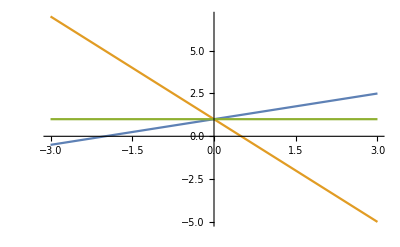

```mathematica
Plot[{0.5x+1,-2x+1,1},{x,-3,3}]
```

b)

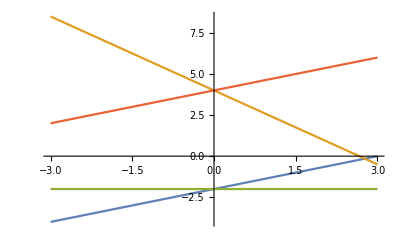

```mathematica
Plot[{2/3 x-2,-3/2 x+4,-2,2/3 x+4},{x,-3,3}]
```

c)

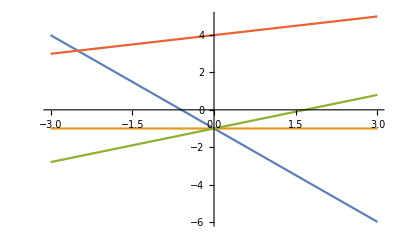

```mathematica
Plot[{-5/3 x-1,-1,3/5 x-1,1/3 x+4},{x,-3,3}]
```

d)

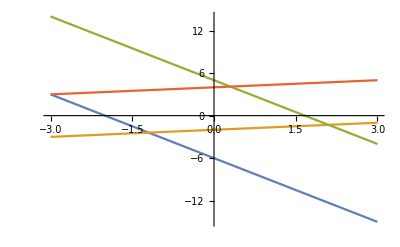

```mathematica
Plot[{-3x-6,1/3 x-2,-3x+5,1/3 x+4},{x,-3,3}]
```

e)

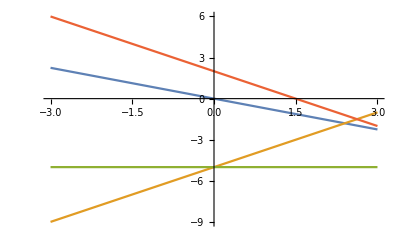

```mathematica
Plot[{-3/4 x,4/3 x-5,-5,-4/3 x+2},{x,-3,3}]
```

f)

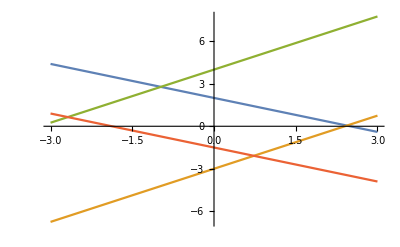

```mathematica
Plot[{-4/5 x+2,5/4 x-3,5/4 x+4,-4/5 x-3/2},{x,-3,3}]
```

9) Izračunaj:
a)

```mathematica
Evaluate[√2*√18]
```

6

b)

```mathematica
Evaluate[√(2*7*7*8)]
```

28

c)

```mathematica
Evaluate[√13*√52]
```

26

d)

```mathematica
Evaluate[√(6/5)*√(5/24)]
```

1/2

e)

```mathematica
Evaluate[√3*√27]
```

9

f)

```mathematica
Evaluate[√(4*10^6)]
```

2000

g)

```mathematica
Evaluate[√8*√72]
```

24

h)

```mathematica
Evaluate[√(11/5)*√(125/11)]
```

5

10) Na avtomobilski prtljažnik, za katerega je največja dovoljena obremenitev 70 kg, bi radi
naložili lesene deske širine 1,2 dm, višine 2 cm in dolžine 3 m. Koliko takih desk lahko
naložimo na prtljažnik, če je gostota suhega lesa 0,5 g/ cm .

```mathematica
Širina = 1.2/10
Višina = 2/100
Dolžina = 3
Gostota = 0.5*1000
```

0.12

1/50

3

500.

```mathematica
Najprej pretvorimo vse v metre in kilograme
```

```mathematica
Volumen = Širina * Višina * Dolžina
```

0.0072

```mathematica
Nato izračunamo volumen.
```

```mathematica
Masa = Volumen * Gostota
```

3.6

```mathematica
Za konec izračunamo maso ene deske. Ugotovimo da je to 3.6 kg.
```

```mathematica
KolikoDesk = 70 / 3.6
```

19.4444

```mathematica
Izračunali smo da lahko na prtljažnik avta spravimo celih 19 desk, preden se bo vdrl.
```